Hopf algebra basics: rooted trees

You don’t need to read the following notes by Foissy, but I refer to them a few times here, for completeness:
http://loic.foissy.free.fr/pageperso/preprint3.pdf

In a way, what I do here is the “complement” of what I did with the symmetric group in finite_groups_basic.nb, where we focused on the cycles (think of the Cayley graph). Here we focus on graphs without cycles, called trees. They are also a special kind of tree graphs: trees that have a root.

```mathematica
Remove["Global`*"]//Quiet
```

Here’s the example in Foissy:

```mathematica
example =TreeGraph[{1->2,1->3,3->4},VertexLabels->Placed["Name",Center],VertexSize->0.3]
```

-Graphics-

This is a Graph data structure, as in finite_groups_basic.nb.
Actually, Tree is its own data structure, in computer science more generally. Think an actual tree with root and branches, but upside down. Or, a family tree going downwards, with grandparent, children, and so on). We convert with GraphTree:

```mathematica
exampleTree = GraphTree[%]
```

-Graphics-

The top node is the root. (Unlike for graphs, Mathematica draws the bottom nodes in trees with a slightly different symbol than the ones higher up in the tree, like  vs. but that’s not important here. Also note the arrows are implicit: always down.)
Internally a Tree data structure is stored by nesting:
 (for more details on this data structure, see below)

```mathematica
InputForm[%]
```

Tree[1, {Tree[2, None], Tree[3, {Tree[4, None]}]}]

where “None” means “no child” (using the terminology of family trees).

Now, to make a bialgebra, we cut the tree branches, and keep the fallen pieces separate from the root-connected piece by the tensor product symbol ⊗. An admissible cut is one where no path through the original tree meets more than one cut. Let’s get started.

Cut the edge 1 -> 2, and put the “pruned” piece that falls down first:

```mathematica
cut1 = {Tree[2,None],TreeDelete[exampleTree,1]}
```

{-Graphics-,-Graphics-}

This is number 4 in Foissy’s table. 
(I did it by hand; below is an automated version.)
It’s not admissible to cut this again (cf. definition of admissible above).
Now cut the edge 1 -> 3:

```mathematica
cut2 = {TreeChildren[exampleTree][[2]],TreeDelete[exampleTree,{2}]}
```

{-Graphics-,-Graphics-}

The above is number 2 in Foissy’s table. 
Disconnected parts are allowed, so we can further cut the edge 1 -> 2 above:

```mathematica
cut3 ={Tree[3,{Tree[4,None]}],{Tree[1,None],Tree[2,None]}}
```

{-Graphics-,{-Graphics-,-Graphics-}}

It can also be grouped like this.

```mathematica
cut4={{Tree[2,None],Tree[3,{Tree[4,None]}]},Tree[1,None]}
```

{{-Graphics-,-Graphics-},-Graphics-}

Note that cutting the edge 3 -> 4 in these last things is not admissible anymore, since we already cut one edge on the same path: 1 -> 3.

There is now only one admissible cut left, that I leave for you as exercise.

The coproduct Δ of the bialgebra is:
e ⊗ t + t ⊗ e + (what falls down ⊗ what is left), 
where “e” is the empty tree. The role of ⊗ is simply to keep the two pieces apart.
This bialgebra becomes Hopf by finding an “inverse”: the antipode s.

First for just a single node •, call it • = a to make it easier to type.

```mathematica
Δa =  e ⊗ a+ a ⊗ e ;
sIdΔa = s[e]⊗ a + s[a] ⊗ e;
ruleμ = {(a_ ⊗ b_)-> a b}; ruleS = s[e]->e; 
sIdΔa  /. rules;
% //.ruleμ 
% ==0/. e->1
Solve[%,s[a]]//First
```

e S(a)+a e

S(a)+a==0

{S(a)→-a}

OK. 
Now the tree with two nodes, call it t. As is intuitive, cutting it produces two pieces a ⊗ a, where again a = •.
The coproduct is:

```mathematica
Δt =  e ⊗ t+ t ⊗ e + a ⊗ a;
sIdΔt = s[e]⊗ t + s[t] ⊗ e +s[a] ⊗ a;
ruleS = {s[e]->e,s[a]->-a};
SIdΔt  /. ruleS
% //.ruleμ 
% ==0/. e->1
Solve[%,s[t]]//First
```

-a⊗a+S(t)⊗e+e⊗t

-a^2+e S(t)+e t

-a^2+S(t)+t==0

{S(t)→a^2-t}

There is a general formula in Foissy, which this can be compared to.
Now some more generic but related comments. 

We can construct binary operations by Groupings.
For example, on four ordered elements a,b,c,d we have:

```mathematica
Groupings[{a,b,c,d},CircleTimes->2]
```

{((a⊗b)⊗c)⊗d,a⊗((b⊗c)⊗d),(a⊗(b⊗c))⊗d,a⊗(b⊗(c⊗d)),(a⊗b)⊗(c⊗d)}

Take the first term. It can be represented as a tree:

((a⊗b)⊗c)⊗d

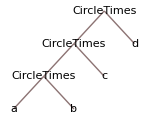

```mathematica
example = %[[1]]
exampleTree = TreeForm[example]
```

At first, it’s easiest to read this from bottom to top. 
More broadly, the importance of this is that symbolic manipulation software like Mathematica in fact stores mathematical expressions as trees internally.

Use one of the predefined graphs as example, here the complete Kary tree (the name doesn’t matter, it’s pretty obvious what it is):

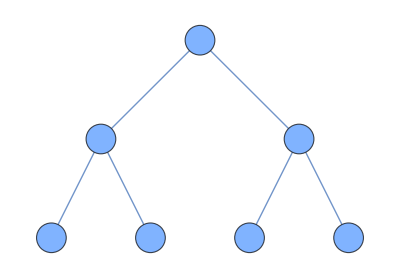

```mathematica
biggerExample = CompleteKaryTree[3,VertexLabels->Placed["Name",Center],VertexSize->0.3]
```

As mentioned above, the “lines” in this Tree data structure aren’t their own objects, so it’s more natural to cut edges in the corresponding Graph:

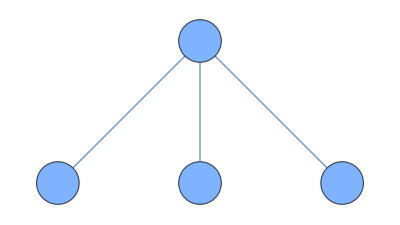
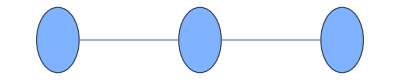

```mathematica
ConnectedGraphComponents[EdgeDelete[biggerExample,{1<-> 3}]]
```

This is the automated cutting procedure, use EdgeDelete.
Again, Graphs don’t have a root, but we can easily display them as Trees:

```mathematica
Map[GraphTree,%]
```

{-Graphics-,-Graphics-}

Notice the difference to the graphs above.
To get the above Hopf algebra, these have to be ordered.

Comment: the Kirchhoff matrix (same as in the circuit laws):

```mathematica
KirchhoffMatrix[biggerExample]//Normal
```

(2 | -1 | -1 | 0 | 0 | 0 | 0
-1 | 3 | 0 | -1 | -1 | 0 | 0
-1 | 0 | 3 | 0 | 0 | -1 | -1
0 | -1 | 0 | 1 | 0 | 0 | 0
0 | -1 | 0 | 0 | 1 | 0 | 0
0 | 0 | -1 | 0 | 0 | 1 | 0
0 | 0 | -1 | 0 | 0 | 0 | 1)

One recent application is solvable quantum circuits:
https://arxiv.org/abs/2409.17215